```mathematica
Quit[]
```

[ Comments ]

-  In  this  notebook, we  attach  the  complete  analytic  expression  of  the  dynamical  matrix  ℳ(ω, k)  as  well  as  the  dispersion  relations  ω (k)  of  the  low-energy  mode  in  low  ω, k  expansion.

-  The  computations  are  explained  in  Section 2  of  the  manuscript.

# Magnetohydrodynamics

### [Part 0] Preliminary : notation

In this note, we use the following notation.

[ Thermodynamic quantity ]
ϵ   =  energy density
p  =  pressure density
T  =  temperature
ρ  =  density
μ  =  chemical potential
B  =  magnetic field

[ Transport coefficient ]
σ  =  conductivity
η  =  shear viscosity

[ Thermodynamic susceptibility ]
dϵodT  =  ((∂ϵ)/(∂T))_(μ, B) ,      dϵodμ  =  ((∂ϵ)/(∂μ))_(T, B) ,     dϵodB  =  ((∂ϵ)/(∂B))_(T, μ) , 
dpodT  =  ((∂p)/(∂T))_(μ, B) ,     dpodμ  =  ((∂p)/(∂μ))_(T, B) ,     dpodB  =  ((∂p)/(∂B))_(T, μ) , 
dρodT  =  ((∂ρ)/(∂T))_(μ, B) ,     dρodμ  =  ((∂ρ)/(∂μ))_(T, B) ,     dρodB  =  ((∂ρ)/(∂B))_(T, μ)  .

[ Others ]
 eb   =   √λ  =  bare electric charge;   λ is the square of the electromagnetic coupling
 ϵe   =  electric permittivity
μm  =  magnetic permeability

### [Part 1] Dynamical Matrix ℳ(ω, k)

Dynamica   Matrix   ℳ (ω, k)

```mathematica
ℳ = {{(dϵodμ k^2 (dρodT T+dρodμ μ) σ)/(dρodμ (-dϵodμ dρodT+dϵodT dρodμ) T)-ⅈ ω,(ⅈ k (dρodμ (p+ϵ)-dϵodμ ρ))/(dϵodμ dρodT-dϵodT dρodμ),-(ⅈ B k (B dρodμ^2 (-eb^2+μm)+eb^2 (-dϵodμ dρodB dρodμ μm+dϵodB dρodμ^2 μm+dϵodμ k^2 σ)))/(dρodμ (-dϵodμ dρodT+dϵodT dρodμ) eb^2 μm),(ⅈ dϵodμ k (dρodμ+k^2 ϵe) σ)/(dρodμ (-dϵodμ dρodT+dϵodT dρodμ)),(ⅈ k (B dρodμ (eb^2-μm)+(dϵodμ dρodB-dϵodB dρodμ) eb^2 μm))/((dϵodμ dρodT-dϵodT dρodμ) eb^2 μm),(dϵodμ dρodB k^2 σ)/(dρodμ (-dϵodμ dρodT+dϵodT dρodμ))},{(ⅈ (dpodμ dρodT-dpodT dρodμ) k)/(dρodμ (p+ϵ)),(k^2 η+B^2 σ)/(p+ϵ)-ⅈ ω,(B dpodμ k^2+B^2 dρodμ μm σ)/(dρodμ p μm+dρodμ ϵ μm),-(dpodμ k^2 ϵe+dρodμ ρ)/(dρodμ p+dρodμ ϵ),-(B σ)/(p+ϵ),-(ⅈ k (B dρodμ (eb^2-μm)+(-dpodμ dρodB+dpodB dρodμ) eb^2 μm))/(dρodμ eb^2 (p+ϵ) μm)},{-(ⅈ B k (dρodT T+dρodμ μ) σ)/(dρodμ T (p+ϵ)),(B ρ)/(p+ϵ),(dρodμ k^2 η μm+B dρodμ μm ρ-B^2 k^2 σ)/(dρodμ p μm+dρodμ ϵ μm)-ⅈ ω,(B (dρodμ+k^2 ϵe) σ)/(dρodμ (p+ϵ)),-ρ/(p+ϵ),-(ⅈ B dρodB k σ)/(dρodμ (p+ϵ))},{-(ⅈ k (dρodT T+dρodμ μ) (B^2+(p+ϵ) μm) σ)/(dρodμ T (p+ϵ) ϵe μm),((B^2+(p+ϵ) μm) ρ)/((p+ϵ) ϵe μm),(B dρodμ μm (k^2 η+B ρ)-B k^2 (B^2+(p+ϵ) μm) σ)/(dρodμ (p+ϵ) ϵe μm^2),((dρodμ+k^2 ϵe) (B^2+(p+ϵ) μm) σ)/(dρodμ (p+ϵ) ϵe μm)-ⅈ ω,-(B ρ)/(p ϵe μm+ϵ ϵe μm),-(ⅈ dρodB k (B^2+(p+ϵ) μm) σ)/(dρodμ (p+ϵ) ϵe μm)},{(ⅈ B k ((dpodμ dρodT-dpodT dρodμ) T (-1+ϵe μm)-B ϵe (dρodT T+dρodμ μ) μm σ))/(dρodμ T (p+ϵ) ϵe μm),(B (k^2 η (-1+ϵe μm)+B ϵe μm ρ-(p+ϵ) μm σ+B^2 (-1+ϵe μm) σ))/((p+ϵ) ϵe μm),(dρodμ (p+ϵ) μm^2 ρ+B^2 (dpodμ k^2 (-1+ϵe μm)+dρodμ ϵe μm^2 ρ)+B^3 μm (-k^2 ϵe+dρodμ (-1+ϵe μm)) σ+B dρodμ μm^2 (k^2 ϵe η-(p+ϵ) σ))/(dρodμ (p+ϵ) ϵe μm^2),(B ((1-ϵe μm) (dpodμ k^2 ϵe+dρodμ ρ)+B ϵe (dρodμ+k^2 ϵe) μm σ))/(dρodμ (p+ϵ) ϵe μm),(-B ϵe μm ρ+B^2 (σ-ϵe μm σ)+(p+ϵ) μm (σ-ⅈ ϵe ω))/((p+ϵ) ϵe μm),-(ⅈ k (dρodμ eb^2 (p+ϵ) μm-B (dpodμ dρodB-dpodB dρodμ) eb^2 μm (-1+ϵe μm)+B^2 (dρodμ (eb^2-μm) (-1+ϵe μm)+dρodB eb^2 ϵe μm^2 σ)))/(dρodμ eb^2 (p+ϵ) ϵe μm^2)},{0,0,ⅈ B k,0,-ⅈ k,-ⅈ ω}};
```

```mathematica
ℳ//MatrixForm
```

((dϵodμ k^2 (dρodT T+dρodμ μ) σ)/(dρodμ (-dϵodμ dρodT+dϵodT dρodμ) T)-ⅈ ω | (ⅈ k (dρodμ (p+ϵ)-dϵodμ ρ))/(dϵodμ dρodT-dϵodT dρodμ) | -(ⅈ B k (B dρodμ^2 (-eb^2+μm)+eb^2 (-dϵodμ dρodB dρodμ μm+dϵodB dρodμ^2 μm+dϵodμ k^2 σ)))/(dρodμ (-dϵodμ dρodT+dϵodT dρodμ) eb^2 μm) | (ⅈ dϵodμ k (dρodμ+k^2 ϵe) σ)/(dρodμ (-dϵodμ dρodT+dϵodT dρodμ)) | (ⅈ k (B dρodμ (eb^2-μm)+(dϵodμ dρodB-dϵodB dρodμ) eb^2 μm))/((dϵodμ dρodT-dϵodT dρodμ) eb^2 μm) | (dϵodμ dρodB k^2 σ)/(dρodμ (-dϵodμ dρodT+dϵodT dρodμ))
(ⅈ (dpodμ dρodT-dpodT dρodμ) k)/(dρodμ (p+ϵ)) | (k^2 η+B^2 σ)/(p+ϵ)-ⅈ ω | (B dpodμ k^2+B^2 dρodμ μm σ)/(dρodμ p μm+dρodμ ϵ μm) | -(dpodμ k^2 ϵe+dρodμ ρ)/(dρodμ p+dρodμ ϵ) | -(B σ)/(p+ϵ) | -(ⅈ k (B dρodμ (eb^2-μm)+(-dpodμ dρodB+dpodB dρodμ) eb^2 μm))/(dρodμ eb^2 (p+ϵ) μm)
-(ⅈ B k (dρodT T+dρodμ μ) σ)/(dρodμ T (p+ϵ)) | (B ρ)/(p+ϵ) | (dρodμ k^2 η μm+B dρodμ μm ρ-B^2 k^2 σ)/(dρodμ p μm+dρodμ ϵ μm)-ⅈ ω | (B (dρodμ+k^2 ϵe) σ)/(dρodμ (p+ϵ)) | -ρ/(p+ϵ) | -(ⅈ B dρodB k σ)/(dρodμ (p+ϵ))
-(ⅈ k (dρodT T+dρodμ μ) (B^2+(p+ϵ) μm) σ)/(dρodμ T (p+ϵ) ϵe μm) | ((B^2+(p+ϵ) μm) ρ)/((p+ϵ) ϵe μm) | (B dρodμ μm (k^2 η+B ρ)-B k^2 (B^2+(p+ϵ) μm) σ)/(dρodμ (p+ϵ) ϵe μm^2) | ((dρodμ+k^2 ϵe) (B^2+(p+ϵ) μm) σ)/(dρodμ (p+ϵ) ϵe μm)-ⅈ ω | -(B ρ)/(p ϵe μm+ϵ ϵe μm) | -(ⅈ dρodB k (B^2+(p+ϵ) μm) σ)/(dρodμ (p+ϵ) ϵe μm)
(ⅈ B k ((dpodμ dρodT-dpodT dρodμ) T (-1+ϵe μm)-B ϵe (dρodT T+dρodμ μ) μm σ))/(dρodμ T (p+ϵ) ϵe μm) | (B (k^2 η (-1+ϵe μm)+B ϵe μm ρ-(p+ϵ) μm σ+B^2 (-1+ϵe μm) σ))/((p+ϵ) ϵe μm) | (dρodμ (p+ϵ) μm^2 ρ+B^2 (dpodμ k^2 (-1+ϵe μm)+dρodμ ϵe μm^2 ρ)+B^3 μm (-k^2 ϵe+dρodμ (-1+ϵe μm)) σ+B dρodμ μm^2 (k^2 ϵe η-(p+ϵ) σ))/(dρodμ (p+ϵ) ϵe μm^2) | (B ((1-ϵe μm) (dpodμ k^2 ϵe+dρodμ ρ)+B ϵe (dρodμ+k^2 ϵe) μm σ))/(dρodμ (p+ϵ) ϵe μm) | (-B ϵe μm ρ+B^2 (σ-ϵe μm σ)+(p+ϵ) μm (σ-ⅈ ϵe ω))/((p+ϵ) ϵe μm) | -(ⅈ k (dρodμ eb^2 (p+ϵ) μm-B (dpodμ dρodB-dpodB dρodμ) eb^2 μm (-1+ϵe μm)+B^2 (dρodμ (eb^2-μm) (-1+ϵe μm)+dρodB eb^2 ϵe μm^2 σ)))/(dρodμ eb^2 (p+ϵ) ϵe μm^2)
0 | 0 | ⅈ B k | 0 | -ⅈ k | -ⅈ ω)

### [Part 2] Dispersion relation at low-(ω, k) expansion : zero density

Magnetosonic waves

 ω = ± v_ms k - ⅈ Γ_ms/2 k^2

```mathematica
vms = (√(B (-dpodT dϵodB+dpodB dϵodT) eb^2 μm+dpodT eb^2 (p+ϵ) μm+B^2 (dpodT eb^2+2 dϵodT eb^2-dpodT μm-dϵodT μm)))/(√dϵodT eb √(B^2+(p+ϵ) μm));
```

```mathematica
Γms = (-B^5 (dpodT dϵodB-dpodB dϵodT) eb^2 μm ((2 dpodT+3 dϵodT) eb^2-2 (dpodT+dϵodT) μm) (-1+ϵe μm)+B^6 (dpodT+dϵodT) (eb^2-μm) ((dpodT+2 dϵodT) eb^2-(dpodT+dϵodT) μm) (-1+ϵe μm)+dpodT dϵodT eb^4 (p+ϵ)^2 η μm^4 σ-B^3 (dpodT dϵodB-dpodB dϵodT) eb^2 μm^2 ((p+ϵ) (2 dpodT μm+2 dϵodT μm-dϵodT eb^2 (2+ϵe μm)+dpodT eb^2 (-3+2 ϵe μm))+dϵodT eb^2 η μm σ)+B (dpodT dϵodB-dpodB dϵodT) eb^4 (p+ϵ) μm^3 (dpodT (p+ϵ)-dϵodT (p+ϵ+η μm σ))+B^2 eb^2 (p+ϵ) μm^2 (dpodT^2 ((p+ϵ) μm-eb^2 (p+ϵ+(dϵodB^2-(p+ϵ) ϵe) μm))+dϵodT^2 (-μm (p+ϵ+η μm σ)+eb^2 (2 p+2 ϵ-dpodB^2 μm+2 η μm σ))-dpodT dϵodT (η μm^2 σ+eb^2 (p+ϵ+p ϵe μm+ϵ ϵe μm-2 μm (dpodB dϵodB+η σ))))+B^4 μm (dpodT^2 ((-p-ϵ) μm^2+eb^4 (2 (p+ϵ)+dϵodB^2 μm) (-1+ϵe μm)-eb^2 (p+ϵ) μm (-3+2 ϵe μm))+dϵodT^2 μm (dpodB^2 eb^4 (-1+ϵe μm)+(2 eb^2-μm) (p+ϵ-eb^2 (p+ϵ) ϵe+eb^2 η σ))+dpodT dϵodT (-2 (p+ϵ) μm^2-eb^2 μm ((p+ϵ) (-5+ϵe μm)+η μm σ)+eb^4 (-4 ϵ+2 dpodB dϵodB μm+2 p (-2+ϵe μm)+μm (2 ϵ ϵe-2 dpodB dϵodB ϵe μm+η σ)))))/(dϵodT eb^2 μm (B^2+(p+ϵ) μm)^2 (B (-dpodT dϵodB+dpodB dϵodT) eb^2 μm+dpodT eb^2 (p+ϵ) μm+B^2 ((dpodT+2 dϵodT) eb^2-(dpodT+dϵodT) μm)) σ);
```

Shear diffusive mode

 ω = - ⅈ D_shear k^2

```mathematica
Dshear = (η μm)/(B^2+(p+ϵ) μm);
```

Magnetic diffusive mode

 ω = - ⅈ D_mag k^2

```mathematica
Dmag = (dpodT eb^2 (p+ϵ))/((B (-dpodT dϵodB+dpodB dϵodT) eb^2 μm+dpodT eb^2 (p+ϵ) μm+B^2 ((dpodT+2 dϵodT) eb^2-(dpodT+dϵodT) μm)) σ);
```

(Two degenerated)Gaps

ω = ω_gap

```mathematica
ωgap = -(ⅈ (B^2+(p+ϵ) μm) σ)/((p+ϵ) ϵe μm);
```

### [Part 3] Dispersion relation at low-(ω, k) expansion : finite density

Longitudinal diffusive mode

 ω = - ⅈ D_long k^2

```mathematica
Dlong = ((p+ϵ) (dpodμ dρodT T-dpodT dρodμ T-(dρodT T+dρodμ μ) ρ) σ)/((dϵodμ dρodT-dϵodT dρodμ) T (ρ^2+B^2 σ^2));
```

Subdiffusive mode

 ω = - ⅈ D_subdiff k^4

```mathematica
Dsubdiff = η/(μm ρ^2);
```

(Four)Gaps

 ω = ω_gap

```mathematica
ωgap = {(-B ρ+ⅈ B^2 σ+ⅈ p μm σ+ⅈ ϵ μm σ-√((B ρ-ⅈ B^2 σ-ⅈ p μm σ-ⅈ ϵ μm σ)^2-4 (-p ϵe μm-ϵ ϵe μm) (μm ρ^2-ⅈ B μm ρ σ)))/(2 (-p ϵe μm-ϵ ϵe μm)),(-B ρ+ⅈ B^2 σ+ⅈ p μm σ+ⅈ ϵ μm σ+√((B ρ-ⅈ B^2 σ-ⅈ p μm σ-ⅈ ϵ μm σ)^2-4 (-p ϵe μm-ϵ ϵe μm) (μm ρ^2-ⅈ B μm ρ σ)))/(2 (-p ϵe μm-ϵ ϵe μm)),(B ρ+ⅈ B^2 σ+ⅈ p μm σ+ⅈ ϵ μm σ-√((-B ρ-ⅈ B^2 σ-ⅈ p μm σ-ⅈ ϵ μm σ)^2-4 (-p ϵe μm-ϵ ϵe μm) (μm ρ^2+ⅈ B μm ρ σ)))/(2 (-p ϵe μm-ϵ ϵe μm)),(B ρ+ⅈ B^2 σ+ⅈ p μm σ+ⅈ ϵ μm σ+√((-B ρ-ⅈ B^2 σ-ⅈ p μm σ-ⅈ ϵ μm σ)^2-4 (-p ϵe μm-ϵ ϵe μm) (μm ρ^2+ⅈ B μm ρ σ)))/(2 (-p ϵe μm-ϵ ϵe μm))};
```

# Quasi-normal modes (Holography) vs. Hydrodynamic predictions

### [Part 4] The unreasonable effectiveness of first-order magnetohydrodynamics

-  Dots  are  numerically  computed  quasi-normal  modes.
-  Solid  lines  are  dispersion relations  computed  by  det[ℳ (ω, k)] = 0  where  ℳ (ω, k)  is  given  in  [Part 1].

#### [Part 4-1] Zero density

-  This  can  be  compared  with  [ Fig. 1 ]  in  the  manuscript.

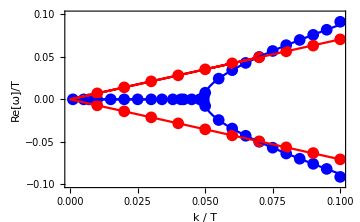
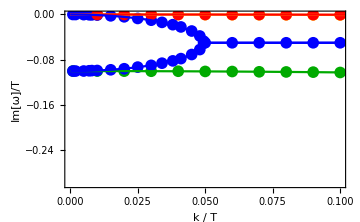

-  This  can  be  compared  with  [ Fig. 2 ]  in  the  manuscript.

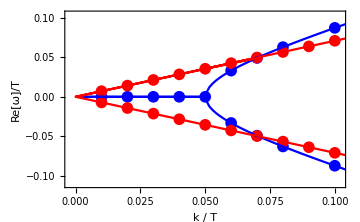
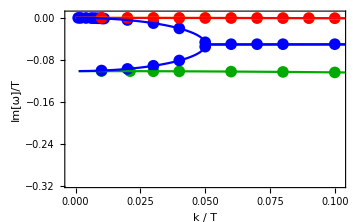
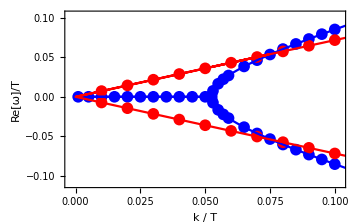
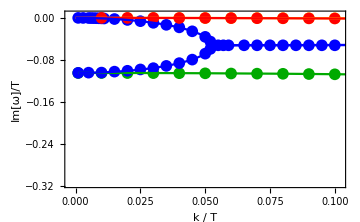

#### [Part 4-2] Finite density

-  This  can  be  compared  with  [ Fig. 3 ]  in  the  manuscript.

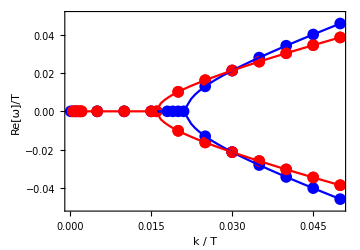
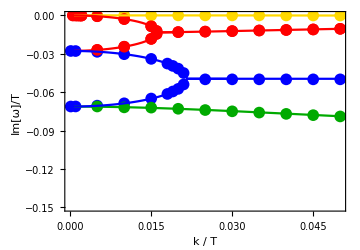
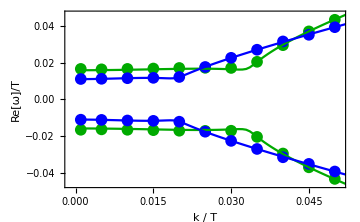
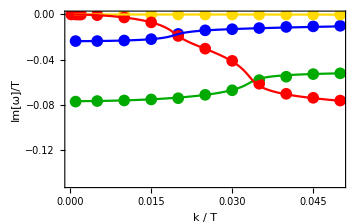

-  This  can  be  compared  with  [ Fig. 4 ]  in  the  manuscript.

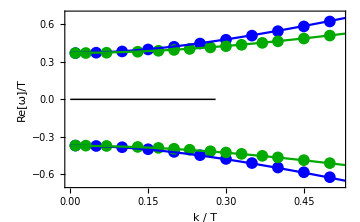
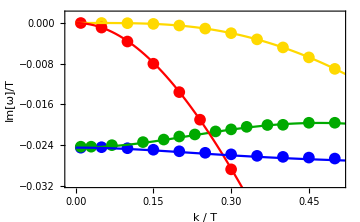
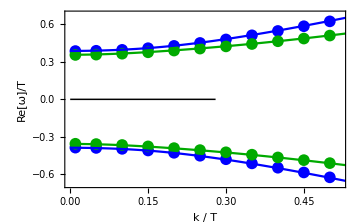
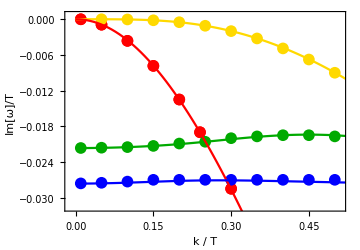

-  This  can  be  compared  with  [ Fig. 5 ]  in  the  manuscript.

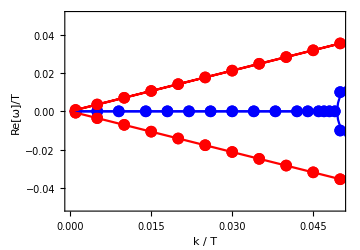
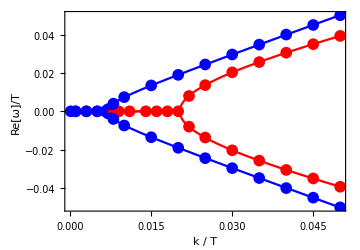
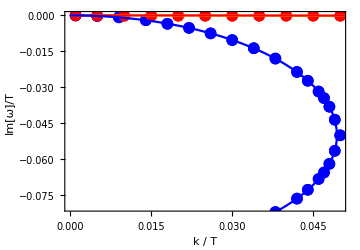
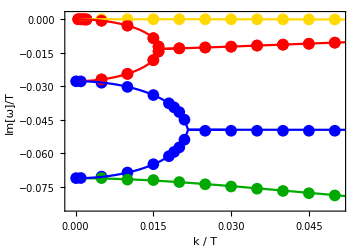
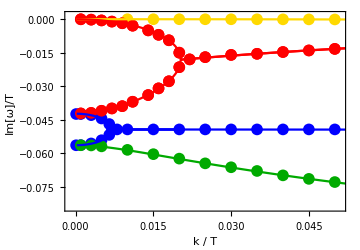
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-

-  This  can  be  compared  with  [ Fig. 6 ]  in  the  manuscript.